```mathematica
N[π,21]
```

3.14159265358979323846

```mathematica
N[ⅇ,21]
```

2.71828182845904523536

```mathematica
note={"F6","D6","G6","D6","A6","E7","E6","B6","A6","F6","A6","D7","E7","C7","E7","F6","E6","F6","D7","G6"}
notee={"E6","C7","D6","D7","E6","D7","D6","D7","E6","D7","G6","A6","E7","C6","G6","A6","E6","F6","A6","F6"}
```

{F6,D6,G6,D6,A6,E7,E6,B6,A6,F6,A6,D7,E7,C7,E7,F6,E6,F6,D7,G6}

{E6,C7,D6,D7,E6,D7,D6,D7,E6,D7,G6,A6,E7,C6,G6,A6,E6,F6,A6,F6}

```mathematica
note[[1]]
```

F6

```mathematica
Table[SoundNote[{note[[2i-1]],note[[2i]]}],{i,1,Floor[Length[note]/2]}]
```

{SoundNote[{F6,D6}],SoundNote[{G6,D6}],SoundNote[{A6,E7}],SoundNote[{E6,B6}],SoundNote[{A6,F6}],SoundNote[{A6,D7}],SoundNote[{E7,C7}],SoundNote[{E7,F6}],SoundNote[{E6,F6}],SoundNote[{D7,G6}]}

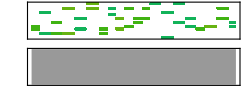

```mathematica
rnd=RandomChoice[{9,10,11,12,13,14,15,25,51},3];
sound=Table[SoundNote[{note[[i]],notee[[i]]},RandomReal[{0.1,0.2}],RandomChoice[rnd]],{i,1,20}];
Sound[sound]
```

```mathematica
Prepend[RandomReal[{0.01,0.05},Length[note]],0]
```

{0,0.030637,0.0263193,0.0238745,0.0380543,0.0400568,0.0188175,0.0417117,0.0157534,0.0168114,0.0471793,0.041122,0.0322605,0.016069,0.0144092,0.0244337,0.0310531,0.0437855,0.016518,0.0175199,0.0183969}

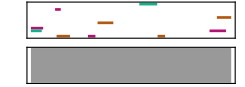

```mathematica
rnd=RandomChoice[{9,10,11,12,13,14,15,25,51},3];
rndtime=Accumulate[Prepend[RandomReal[{0.01,0.05},Length[note]],0]];
rndtimee=Accumulate[Prepend[RandomReal[{0.01,0.05},Length[note]],0]];
sound=Table[{SoundNote[note[[i]],{rndtime[[i]],rndtime[[i+1]]},RandomChoice[rnd]],SoundNote[notee[[i]],{rndtimee[[i]],rndtimee[[i+1]]},RandomChoice[rnd]]},{i,1,5}];
Sound[sound]
```

```mathematica
sound
```

{{SoundNote[F6,{0,0.0329978},11],SoundNote[E6,{0,0.0292248},12]},{SoundNote[D6,{0.0329978,0.0693577},10],SoundNote[C7,{0.0292248,0.0445679},11]},{SoundNote[G6,{0.0693577,0.112039},10],SoundNote[D6,{0.0445679,0.0648447},11]},{SoundNote[D6,{0.112039,0.132408},10],SoundNote[D7,{0.0648447,0.113509},12]},{SoundNote[A6,{0.132408,0.171305},10],SoundNote[E6,{0.113509,0.158121},11]}}

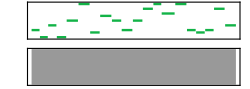

```mathematica
rnd={59};
sound=Table[SoundNote[note[[i]],RandomReal[{0.1,0.2}],RandomChoice[rnd]],{i,1,Length[note]}];
Sound[sound]
```

```mathematica
rnd
```

{11,30,24,26,15}